### 特異積分

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../mathematica_utilities/mathematica_plot_options.nb"}]]

etaSing=1;
Eta[u_,β_,etaSing_]:=etaSing+Sign[u]Sqrt[u^2]^β;
EtaInv[eta_,β_,etaSing_]:=Sign[eta-etaSing]*Sqrt[(eta-etaSing)^2]^(1/β);

Eta0=-1;
Eta1=1;

Manipulate[
tab1=Table[{u,Eta[u,β,etaSing]},{u,EtaInv[Eta0,β,etaSing],EtaInv[Eta1,β,etaSing],(EtaInv[Eta1,β,etaSing]-EtaInv[Eta0,β,etaSing])/20}];
tab2=Table[{eta,EtaInv[eta,β,etaSing]},{eta,Eta0,Eta1,(Eta1-Eta0)/20}];
Row[
{ListPlot[tab1,
Epilog->Table[Line[{{#1,-10},{#1,#2},{-10,#2}}]&@@tab1[[n]],{n,1,Length[tab1]}],
FrameLabel->framelabel["u","η"],
Evaluate[plot2Doption],
PlotLabel->β,
PlotRange->{{EtaInv[Eta0,β,etaSing],EtaInv[Eta1,β,etaSing]},{Eta0,Eta1}},
Mesh->All],
ListPlot[tab2,
Epilog->Table[Line[{{#1,-10},{#1,#2},{-10,#2}}]&@@tab2[[n]],{n,1,Length[tab2]}],
FrameLabel->framelabel["η","u"],
Evaluate[plot2Doption],
PlotRange->{{Eta0,Eta1},{EtaInv[Eta0,β,etaSing],EtaInv[Eta1,β,etaSing]}},
Mesh->All]}
],{β,1/5,5},{etaSing,-1,1}]
```

framelabel[x_,y_,size_:20]

plot2Doption

importData

jsonInfo

interpolateAndFourier

```mathematica
plot[filename_]:=Module[{f0,f1,data},
data=Import[FileNameJoin[{NotebookDirectory[],filename}]];
f0=ListPlot[{{#1,#2}&@@@data,{#1,#3}&@@@data},
GridLines->All,
Joined->True,
PlotLabel->filename,
Evaluate[plot2Doption],
FrameLabel->framelabel["Number of points","Integration"]
];
f1=ListPlot[{#1,#4}&@@@data,
GridLines->All,
Joined->True,
PlotLabel->filename,
Evaluate[plot2Doption],
FrameLabel->framelabel["Number of points","log10|error|"]
];
Return[Row[{f0,f1}]];
]

plotOverlap[filenames_,slot_:2]:=Module[{f0,f1,data1,data2,n},
n=Length[filenames];
ListPlot[Table[{#1,Slot[slot]}&@@@Import[FileNameJoin[{NotebookDirectory[],filenames[[i]]}]],{i,1,n,1}],
GridLines->All,
Joined->True,
(*PlotStyle->{Red,Blue},*)
Evaluate[plot2Doption],
FrameLabel->framelabel["Number of points","Integration"],
PlotLegends->Placed[filenames,Right],
(*PlotLabel->Table[filenames[[i]],{i,1,n,1}],*)
LabelStyle->Directive[FontSize->10],
ImageSize->800
]
]
```

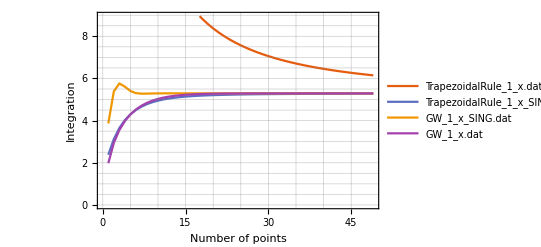
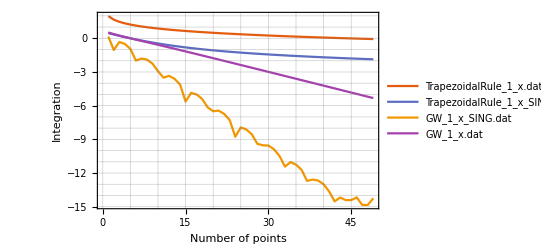

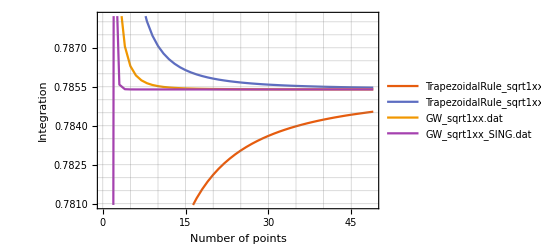
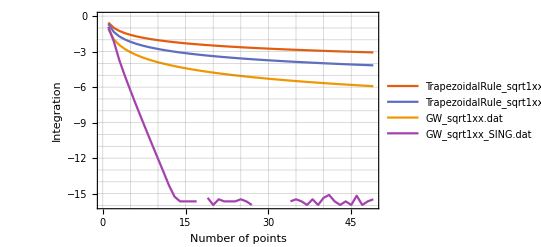

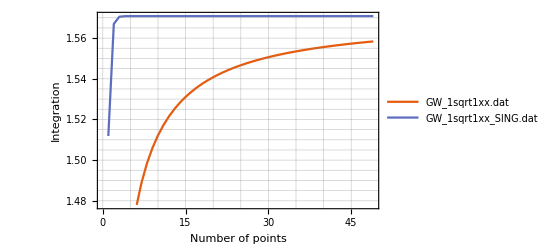
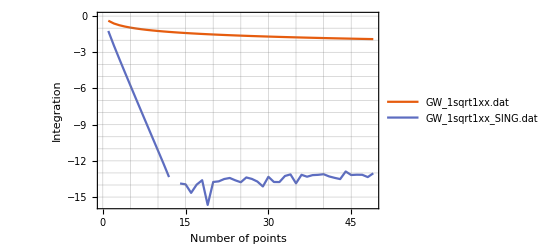

```mathematica
Row[{plotOverlap[{"TrapezoidalRule_1_x.dat","TrapezoidalRule_1_x_SING.dat","GW_1_x_SING.dat","GW_1_x.dat"},2],
plotOverlap[{"TrapezoidalRule_1_x.dat","TrapezoidalRule_1_x_SING.dat","GW_1_x_SING.dat","GW_1_x.dat"},4]}]

Row[{plotOverlap[{"TrapezoidalRule_sqrt1xx.dat","TrapezoidalRule_sqrt1xx_SING.dat","GW_sqrt1xx.dat","GW_sqrt1xx_SING.dat"},2],
plotOverlap[{"TrapezoidalRule_sqrt1xx.dat","TrapezoidalRule_sqrt1xx_SING.dat","GW_sqrt1xx.dat","GW_sqrt1xx_SING.dat"},4]}]

Row[{plotOverlap[{(*"TrapezoidalRule_1sqrt1xx.dat","TrapezoidalRule_1sqrt1xx_SING.dat",*)"GW_1sqrt1xx.dat","GW_1sqrt1xx_SING.dat"},2],
plotOverlap[{(*"TrapezoidalRule_1sqrt1xx.dat","TrapezoidalRule_1sqrt1xx_SING.dat",*)"GW_1sqrt1xx.dat","GW_1sqrt1xx_SING.dat"},4]}]
```

## ルジャンドル関数の結果

#### c++ プログラム（ルジャンドル関数とその微分の計算）が正しいことを確認する

framelabel[x_,y_,size_:20]

plot2Doption

importData

jsonInfo

interpolateAndFourier

10

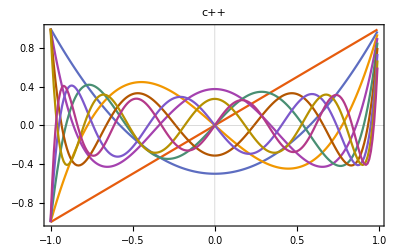
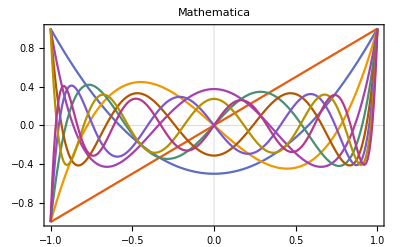

Power::infy: 無限式1/0.^0.5が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.^0.5が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.^0.5が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

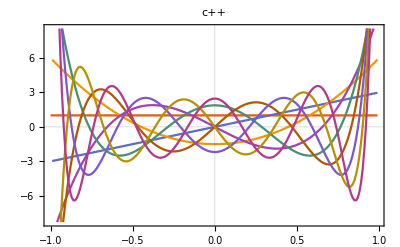
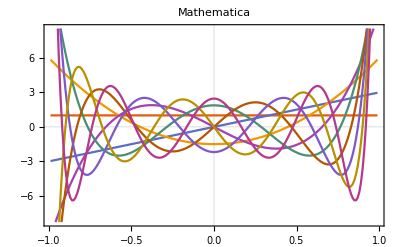

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../mathematica_utilities/mathematica_plot_options.nb"}]]
data=Import[FileNameJoin[{NotebookDirectory[],"LegendrePolynomials.dat"}]];

upto=Length[data[[1]]]

Row[
{
ListPlot[Table[Transpose@{data[[;;,1]],data[[;;,i]]},{i,2,upto}],
Evaluate[plot2Doption],
PlotLabel->"c++"
]
,
ListPlot[Table[Table[{x,LegendreP[n,x]},{x,-1,1,0.01}],{n,1,upto-1}],
Evaluate[plot2Doption],
PlotLabel->"Mathematica"
]}
]


data=Import[FileNameJoin[{NotebookDirectory[],"LegendrePolynomials_D.dat"}]];

(*DL[n_,x_]=D[LegendreP[n,X],X]/.X->x;*)
DL[n_,x_,derorder_:1]=LegendreP[n,derorder,x]*(1-x*x)^(-0.5*derorder)*((-1)^derorder(*c++ではいらない係数*));


Row[
{
ListPlot[Table[Transpose@{data[[;;,1]],data[[;;,i]]},{i,2,upto}],
Evaluate[plot2Doption],
PlotLabel->"c++"
],
ListPlot[Table[Table[{x,DL[n,x]},{x,-1,1,0.01}],{n,1,upto-1}],
Evaluate[plot2Doption],
PlotLabel->"Mathematica"
]
}
]
```

#### 良い初期値の計算

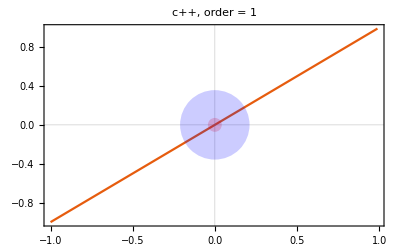
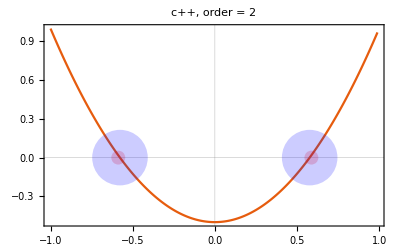
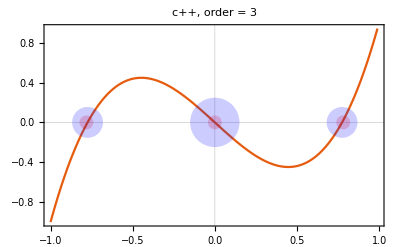
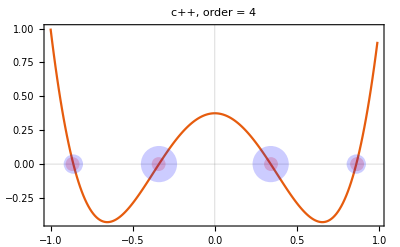
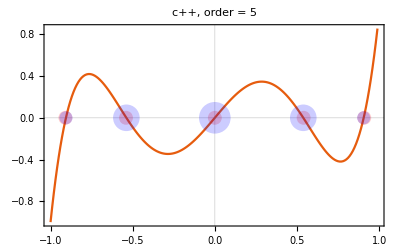
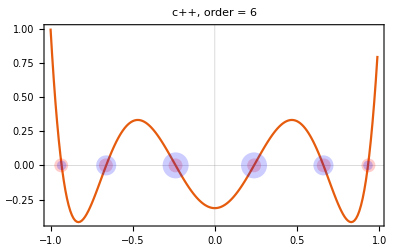
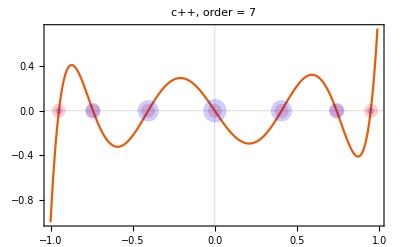
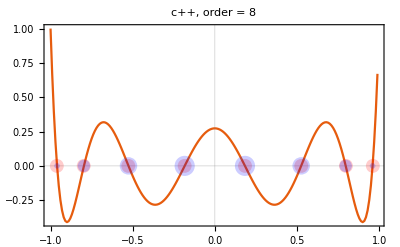

```mathematica
(*微分が正しく計算できているので，Newton法で根を見つけることができる．*)
guess[n_]:=Module[{vec},
vec=Table[Sin[π*(n+1-2*i)/(2n+1)],{i,1,If[EvenQ[n],n/2,(n+1)/2]}];
Return[Join[If[EvenQ[n],-vec,-vec[[;;-2]]],vec]];
]

firstguess=Import[FileNameJoin[{NotebookDirectory[],"first_guess.dat"}]];
roots=Import[FileNameJoin[{NotebookDirectory[],"LegendrePolynomials_roots.dat"}]];
data=Import[FileNameJoin[{NotebookDirectory[],"LegendrePolynomials.dat"}]];
weight=Import[FileNameJoin[{NotebookDirectory[],"LegendrePolynomials_weight.dat"}]];

Row@Table[
ListPlot[Transpose@{data[[;;,1]],data[[;;,1+order]]},
Evaluate[plot2Doption],
Epilog->Append[
Table[{Red,Opacity[0.2],PointSize[0.025],Point[{firstguess[[order]][[p]],0}]},{p,1,Length[firstguess[[order]]]}],
Table[{Blue,Opacity[0.2],PointSize[weight[[order]][[p]]*0.5],Point[{roots[[order]][[p]],0}]},{p,1,Length[roots[[order]]]}]],
PlotLabel->"c++, order = "<>ToString[order]
],{order,1,9}]

(*良い初期値を与えることがわかる*)
```

```mathematica
Column@Table[
Table[{roots[[n]][[i]],LegendreP[n,firstguess[[n]][[i]]]},{i,1,n}]
,{n,1,7}]

(*Newton法によって，first guess が修正され，関数がほぼゼロを返している*)

Column@Table[
Table[{roots[[n]][[i]][[]],LegendreP[n,roots[[n]][[i]]]},{i,1,n}]
,{n,1,7}]

Column@Table[
Table[{roots[[n]][[i]],weight[[n]][[i]]},{i,1,n}]
,{n,1,7}]
```

{{0,0}}
{{-0.57735,0.0182368},{0.57735,0.0182368}}
{{-0.774597,0.022008},{0,0},{0.774597,-0.022008}}
{{-0.861136,0.0234355},{-0.339981,-0.00379977},{0.339981,-0.00379977},{0.861136,0.0234355}}
{{-0.90618,0.0241346},{-0.538469,-0.00527681},{0,0},{0.538469,0.00527681},{0.90618,-0.0241346}}
{{-0.93247,0.0245255},{-0.661209,-0.00601922},{-0.238619,0.00148373},{0.238619,0.00148373},{0.661209,-0.00601922},{0.93247,0.0245255}}
{{-0.949108,0.0247782},{-0.741531,-0.00644886},{-0.405845,0.00223428},{0,0},{0.405845,-0.00223428},{0.741531,0.00644886},{0.949108,-0.0247782}}

{{0,0}}
{{-0.57735,1.96782×10^-16},{0.57735,1.96782×10^-16}}
{{-0.774597,1.31188×10^-15},{0,0},{0.774597,-1.31188×10^-15}}
{{-0.861136,1.67265×10^-15},{-0.339981,5.4115×10^-16},{0.339981,5.4115×10^-16},{0.861136,1.67265×10^-15}}
{{-0.90618,-1.57426×10^-16},{-0.538469,-1.57426×10^-16},{0,0},{0.538469,1.57426×10^-16},{0.90618,1.57426×10^-16}}
{{-0.93247,-7.87128×10^-16},{-0.661209,1.50866×10^-15},{-0.238619,9.8391×10^-17},{0.238619,9.8391×10^-17},{0.661209,1.50866×10^-15},{0.93247,-7.87128×10^-16}}
{{-0.949108,-5.73479×10^-15},{-0.741531,-1.79915×10^-15},{-0.405845,3.65452×10^-16},{0,0},{0.405845,-3.65452×10^-16},{0.741531,1.79915×10^-15},{0.949108,5.73479×10^-15}}

{{0,2}}
{{-0.57735,1},{0.57735,1}}
{{-0.774597,0.555556},{0,0.888889},{0.774597,0.555556}}
{{-0.861136,0.347855},{-0.339981,0.652145},{0.339981,0.652145},{0.861136,0.347855}}
{{-0.90618,0.236927},{-0.538469,0.478629},{0,0.568889},{0.538469,0.478629},{0.90618,0.236927}}
{{-0.93247,0.171324},{-0.661209,0.360762},{-0.238619,0.467914},{0.238619,0.467914},{0.661209,0.360762},{0.93247,0.171324}}
{{-0.949108,0.129485},{-0.741531,0.279705},{-0.405845,0.38183},{0,0.417959},{0.405845,0.38183},{0.741531,0.279705},{0.949108,0.129485}}

```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"BEM_integration_accuracy_check.dat"}]];
Show[
ListContourPlot3D[data,Contours->8,PlotLegends->"Expressions",PlotRange->{Automatic,Automatic,Automatic(*{-3,0}*)}],
Graphics3D[{Red,Line[{{Cos[2Pi/3],Sin[2Pi/3],0},{Cos[4Pi/3],Sin[4Pi/3],0},{Cos[6Pi/3],Sin[6Pi/3],0},{Cos[2Pi/3],Sin[2Pi/3],0}}]}]
]
```

-Graphics3D-